# Beugung

```mathematica
Clear["Global`*"];
```

## Messung

```mathematica
y = {{22.1, 22.7},
{23.7, 24.6},
{25.1, 25.7},
{25.8, 26.5},
{30.7, 31.7},
{36.1, 37.4},
{38.7, 40.0}};
```

```mathematica
y = Table[(y[[i]][[1]]+y[[i]][[2]])/2, {i, 1, Length[y]}]
```

{22.4,24.15,25.4,26.15,31.2,36.75,39.35}

```mathematica
d = 80;
```

```mathematica
l = {7065, 6678, 5875, 5015, 4921, 4713, 4471};
```

```mathematica
g[x_, ll_] = ll/Sin[ArcTan[x/d]];
```

```mathematica
Table[g[y[[i]], l[[Length[l]-i+1]]]*10^-10, {i, 1, Length[l]}]
```

{1.6582×10^-6,1.63083×10^-6,1.62617×10^-6,1.61411×10^-6,1.61692×10^-6,1.59976×10^-6,1.60069×10^-6}

```mathematica
g1 = Mean[%]
```

1.62095×10^-6

## Mikroskop

```mathematica
n = 12;
```

```mathematica
d2 = 0.0208;
```

```mathematica
g2 = d2/n/1000
```

1.73333×10^-6

```mathematica
g=(g2+g1)/2
```

1.67714×10^-6

```mathematica
Abs[(g1-g2)/g]
```

0.0670063

## H

```mathematica
rot= {34.6,35.4}
```

{34.6,35.4}

```mathematica
blau = {24.5 , 25.4}
```

{24.5,25.4}

```mathematica
lambdarot = g*Sin[ArcTan[Mean[rot]/d]]
```

6.72231×10^-7

```mathematica
lambdablau = g*Sin[ArcTan[Mean[blau]/d]]
```

4.99338×10^-7

```mathematica
h = 6.63*10^-34;
```

```mathematica
c=2.99*10^8;
```

2.99×10^8

```mathematica
e = 1.602*10^-19;
```

```mathematica
EE[v_] = h*c/v;
```

```mathematica
EE[lambdarot]/e
```

1.84079

3>2

```mathematica
EE[lambdablau]/e
```

2.47815

4 > 2

```mathematica
En[n_] = -12.6/n^2;
```

```mathematica
En[3] - En[2]
```

1.75

```mathematica
En[4] - En[2]
```

2.3625

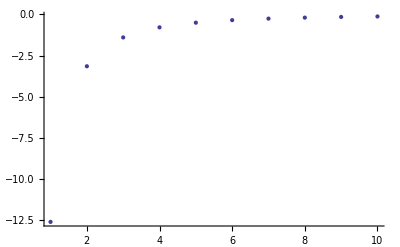

```mathematica
ListPlot[Table[En[n], {n, 1, 10}]]
```